```mathematica
Clear["Global'*"]
```

```mathematica
Factor[s^3+7 s^2+14s+8]
```

(1+s) (2+s) (4+s)

```mathematica
Factor[s^3+s^2-2s-5]
```

-5-2 s+s^2+s^3

```mathematica
FullSimplify[(s^3+s^2-2s-5)/(s^3+7 s^2+14s+8)]
```

(-5+s (-2+s+s^2))/((1+s) (2+s) (4+s))

```mathematica
Factor[2 s^2+7s+7]
```

7+7 s+2 s^2

```mathematica
A=({{-1, 0, 0}, {0, -2, 0}, {0, 0, -4}});
B=({{1}, {1}, {1}});
c1=({{-1, 5/2, -15/2}});
D1=({{1}});
y0=({{1}, {0}, {0}});
u0=({{1}, {0}, {0}});
EA[t_]:={{ⅇ^-t,0,0},{0,ⅇ^(-2 t),0},{0,0,ⅇ^(-4 t)}}
t21=c1.B;
t31=c1.A.B;
s21=c1.A;
s31=c1.A^2;
```

```mathematica
x0=Inverse[({{c1[[1,1]], c1[[1,2]], c1[[1,3]]}, {s21[[1,1]], s21[[1,2]], s21[[1,3]]}, {s31[[1,1]], s31[[1,2]], s31[[1,3]]}})].(y0-(({{D1[[1,1]], 0, 0}, {t21[[1,1]], D1[[1,1]], 0}, {t31[[1,1]], t21[[1,1]], D1[[1,1]]}}).u0))
```

{{-10/3},{-4/5},{8/45}}

```mathematica
ψ1=c1.EA[t].x0;
ψ2=Integrate[c1.EA[t-τ].B,{τ,0,t}];
```

```mathematica
y1[t_]=FullSimplify[((ψ1+ψ2+D1[[1,All]])[[1,All]])[[1,All]]]
y2[t_]=FullSimplify[InverseLaplaceTransform[(s^3+s^2-2s-5)/(s(s^3+7 s^2+14s+8))+(6s+16)/(s^3+7 s^2+14s+8),s,t]]
```

1/24 (-15+13 ⅇ^(-4 t) (1-6 ⅇ^(2 t)+8 ⅇ^(3 t)))

1/24 (-15+13 ⅇ^(-4 t) (1-6 ⅇ^(2 t)+8 ⅇ^(3 t)))

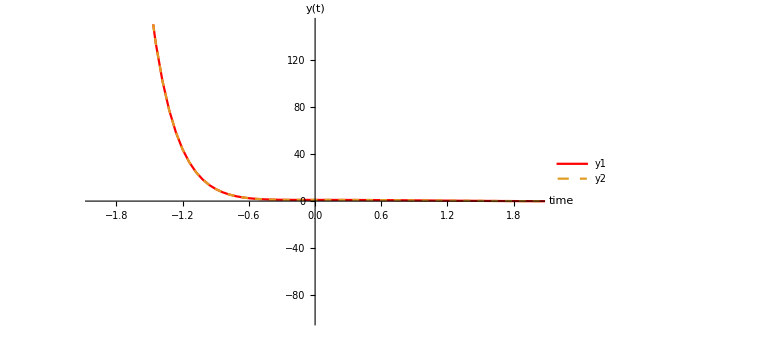

```mathematica
Plot[{y1[t],y2[t]},{t,-100,100},PlotRange->{{-2,2},{-100,1.5*100}},PlotStyle->{Red,Dashed},AxesLabel->{"time","y(t)"},AxesOrigin->{0,0},ImageSize->Large,PlotLegends->{"y1","y2"}]
```

```mathematica
Apart[(s^3+s^2-2s-5)/(s^3+7 s^2+14s+8),s]
```

1-1/(1+s)+5/(2 (2+s))-15/(2 (4+s))

```mathematica
Apart[(6 s^2+16s+13)/(s^3+7 s^2+14s+8),s]
```

1/(1+s)-5/(2 (2+s))+15/(2 (4+s))

```mathematica
Apart[(s^3+s^2-2s-5)/(s*(s^3+7 s^2+14s+8)),s]
```

-5/(8 s)+1/(1+s)-5/(4 (2+s))+15/(8 (4+s))

```mathematica
InverseLaplaceTransform[-5/(8 s)+1/(1+s)-5/(4 (2+s))+15/(8 (4+s)),s,t]
```

-5/8+(15 ⅇ^(-4 t))/8-(5 ⅇ^(-2 t))/4+ⅇ^-t

```mathematica
Apart[(6s+16)/(s^3+7 s^2+14s+8),s]
```

10/(3 (1+s))-2/(2+s)-4/(3 (4+s))

```mathematica
Exp[A*t]
```

{{ⅇ^-t,1,1},{1,ⅇ^(-2 t),1},{1,1,ⅇ^(-4 t)}}